```mathematica
Clear[ζ,ω0]
sol=Simplify[DSolve[{x''[t]+x'[t]2 ω0 ζ+ω0^2 x[t]==0,x[0]==1,x'[0]==0},x,t]];
Simplify[x[t]/.sol,{ω0>0,ζ>0,t>0}]
```

{1/(2 (-1+ζ^2))ⅇ^(-t (ζ+√(-1+ζ^2)) ω0) (-1+ζ^2-ζ √(-1+ζ^2)+ⅇ^(2 t √(-1+ζ^2) ω0) (-1+ζ^2+ζ √(-1+ζ^2)))}

```mathematica
f[x_]=(a x^3+b x^2+c x +d)/ei;
sol=Solve[{(D[f[x],{x,1}]/.x->l)==Sin[θ2],(D[f[x],{x,1}]/.x->0)==Sin[θ1 ],
(D[f[x],{x,0}]/.x->0)==0,(D[f[x],{x,0}]/.x->l)==0},{a,b,c,d}];
(* Torque *)
Simplify[-D[f[x] e l^4,{x,2}]/.sol[[1]]/.x->{0,l}]
(* shear force *)
Simplify[-D[f[x] e l^4,{x,3}]/.sol[[1]]/.x->{0,l}]
(* energy *)
Simplify[-1/2e l^4 Integrate[D[f[x] ,{x,2}]^2,{x,0,l}]/.sol[[1]]]
```

{2 e l^3 (2 Sin[θ1]+Sin[θ2]),-2 e l^3 (Sin[θ1]+2 Sin[θ2])}

-6 e l^2 (Sin[θ1]+Sin[θ2])

-2 e l^3 (Sin[θ1]^2+Sin[θ1] Sin[θ2]+Sin[θ2]^2)

```mathematica
({{Cos[θ], -Sin[θ]}, {Sin[θ], Cos[θ]}})/.θ->π/2//MatrixForm
```

(0 | -1
1 | 0)

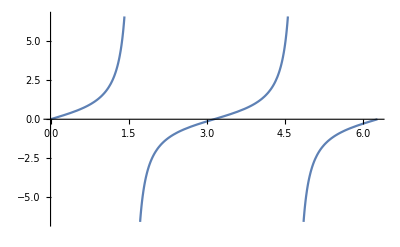

```mathematica
Plot[Tan[θ+π],{θ,0,2π}]
```

```mathematica
X1  = {x1[t],y1[t]};
X2 = {x2[t],y2[t]};
eq={D[X1,{t,2}]==((-(X1-X2))/((X1-X2).(X1-X2))((X1-X2).(X1-X2)-x0))κ,D[X2,{t,2}]==((X1-X2)/((X1-X2).(X1-X2))((X1-X2).(X1-X2)-x0))κ,
(X1/.t->0)=={-1,0},(X2/.t->0)=={1,0},
(D[X1,{t,1}]/.t->0)=={0,1},(D[X2,{t,1}]/.t->0)=={0,-1}}
sol=Simplify[DSolve[eq,{x1,y1,x2,y2},t]]/.{κ->(2π)^2,x0->2}
ParametricPlot[{{x1[t],y1[t]},{x2[t],y2[t]}}/.sol,{t,0,10}]
```

{{x1''[t],y1''[t]}=={-(κ (x1[t]-x2[t]) (-x0+(x1[t]-x2[t])^2+(y1[t]-y2[t])^2))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2),-(κ (-x0+(x1[t]-x2[t])^2+(y1[t]-y2[t])^2) (y1[t]-y2[t]))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)},{x2''[t],y2''[t]}=={(κ (x1[t]-x2[t]) (-x0+(x1[t]-x2[t])^2+(y1[t]-y2[t])^2))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2),(κ (-x0+(x1[t]-x2[t])^2+(y1[t]-y2[t])^2) (y1[t]-y2[t]))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)},{x1[0],y1[0]}=={-1,0},{x2[0],y2[0]}=={1,0},{x1'[0],y1'[0]}=={0,1},{x2'[0],y2'[0]}=={0,-1}}

DSolve[{{x1''[t],y1''[t]}=={-(4 π^2 (x1[t]-x2[t]) (-2+(x1[t]-x2[t])^2+(y1[t]-y2[t])^2))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2),-(4 π^2 (-2+(x1[t]-x2[t])^2+(y1[t]-y2[t])^2) (y1[t]-y2[t]))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)},{x2''[t],y2''[t]}=={(4 π^2 (x1[t]-x2[t]) (-2+(x1[t]-x2[t])^2+(y1[t]-y2[t])^2))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2),(4 π^2 (-2+(x1[t]-x2[t])^2+(y1[t]-y2[t])^2) (y1[t]-y2[t]))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)},{x1[0],y1[0]}=={-1,0},{x2[0],y2[0]}=={1,0},{x1'[0],y1'[0]}=={0,1},{x2'[0],y2'[0]}=={0,-1}},{x1,y1,x2,y2},t]

-Graphics-

```mathematica
D[ArcSin[x],x]
```

1/(√(1-x^2))

```mathematica
AbsSquared[x_]:=x[[1]]^2+x[[2]]^2
abs[x_]:=√AbsSquared[x]
H:=1/(2 m2)AbsSquared[p1]+1/(2 m2)AbsSquared[p2]+1/(2 I1) ω1^2+1/(2 I2)ω2^2+
κ/2(abs[q1-q2]-l)^2+σ/2(θ1 - θ2 + 2 ϕ)^2
assum = {q1x ∈ Reals,q1y ∈ Reals,q2x ∈ Reals,q2y ∈ Reals,
p1x ∈ Reals,p1y ∈ Reals,p2x ∈ Reals,p2y ∈ Reals,
θ1 ∈ Reals,θ2∈ Reals};
```

```mathematica
p1={p1x, p1y};p2={p2x,p2y};q1={q1x, q1y};q2={q2x, q2y};ϕ=ArcTan[(q2y - q1y)/(q2x - q1x)];
Simplify[H,assum]
F=FullSimplify[-D[H,{{q1x,q1y,q2x,q2y,θ1,θ2}}],assum]
FullSimplify[D[H,{{p1x,p2x,p1y,p2y,ω1,ω2}}],assum]
```

H

{0,0,0,0,0,0}

{0,0,0,0,0,0}

```mathematica
Simplify[{F[[1]]+F[[3]]}];
{F[[1]],F[[2]]};
{F[[5]],F[[6]]}
```

{0,0}

```mathematica
Series[FullSimplify[D[ArcSin[x1[t]/((x1[t])^2+(y1[t])^2)],t]],
```

((-x1[t]^2+y1[t]^2) x1'[t]-2 x1[t] y1[t] y1'[t])/((x1[t]^2+y1[t]^2)^2 √(1-x1[t]^2/((x1[t]^2+y1[t]^2)^2)))